```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ClearAll[   eqn,sol,kappa,T0,E0,a, b, X0rad, Lx, Ly, Lz, x0,y0,z0,sx, sy,x,y,z, tungstenRectangularRegion,tungstenMeshRegion,powerDensity3D,powerDensityFun3D]
```

```mathematica
$Assumptions=Lx∈Reals&&Lx>0&&Ly∈Reals&&Ly>0&&Lz∈Reals&&Lz>0 &&x0∈Reals&&y0∈Reals&& z0∈Reals&&sx∈Reals&&sx>0 &&sy∈Reals&&sy>0 &&E0∈Reals&&E0>0&&a∈Reals&&a>0&&b∈Reals&&b>0&&X0rad∈Reals&&X0rad>0;
```

```mathematica
powerDensity3DFunc[x_,y_,z_]:= E0*Exp[- ((x-x0)^2/(2*sx^2)+(y-y0)^2/(2*sy^2))]*b*((b*z/X0rad)^(a-1)*Exp[-b* z/X0rad])/Gamma[a] ;
```

```mathematica
(*powerDensity3DFunc[x_,y_,z_]:= Piecewise[{{E0*Exp[- ((x-x0)^2/(2*sx^2)+(y-y0)^2/(2*sy^2))]*b*((b*z)^(a-1)*Exp[-b*z])/Gamma[a],x0-Lx/2≤x≤x0+Lx/2&&y0-Ly/2≤y≤y0+Ly/2&&z0-Lz/2≤z≤z0+Lz/2}},0];*)
```

```mathematica
NormIntegral=Integrate[powerDensity3DFunc[x,y,z],{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]
```

(2 E0 π sx sy X0rad Erf[Lx/(2 √2 sx)] Erf[Ly/(2 √2 sy)] (Gamma[a,-(b (Lz-2 z0))/(2 X0rad)]-Gamma[a,(b (Lz+2 z0))/(2 X0rad)]))/Gamma[a]

```mathematica
(*The water temperature Tim is using in ANSYS is at 35 degrees. With 0.5 W/cm2/K conductivity between water and copper and using the surface area of the sides of the tungsten block ,we get 16 degrees drop between water and copper. If we get another 9 degrees temperature drop in the copper layer plus the the copper-tungsten interface, we would have 25 degree temperature difference between water and tungsten outer layer. That is, the tungsten boundary will be at 60 degrees if the water is at 35 degrees. *)
```

```mathematica
kappa=0.00150;T0=60;Ptot=6.0; minPower=0.00001;
E0=1;a=5.0;b=0.5; X0rad=0.35;
Lx=15.25;Ly=14.25;Lz=10;
x0=0;y0=0;z0=Lz/2;sx=1.5;sy=1.5;
```

```mathematica
(*powerDensity3D[x_,y_,z_]:= Ptot/NormIntegral*powerDensity3DFunc[x,y,z];*)
```

```mathematica
powerDensity3D[x_,y_,z_]:= Piecewise[{{Ptot/NormIntegral*powerDensity3DFunc[x,y,z], powerDensity3DFunc[x,y,z]>minPower}}, 0];
Ptot
```

6.

```mathematica
NormIntegral
```

4.94077

```mathematica
NIntegrate[powerDensity3D[x,y,z],{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.99824 and 0.0000902283 for the integral and error estimates.

5.99824

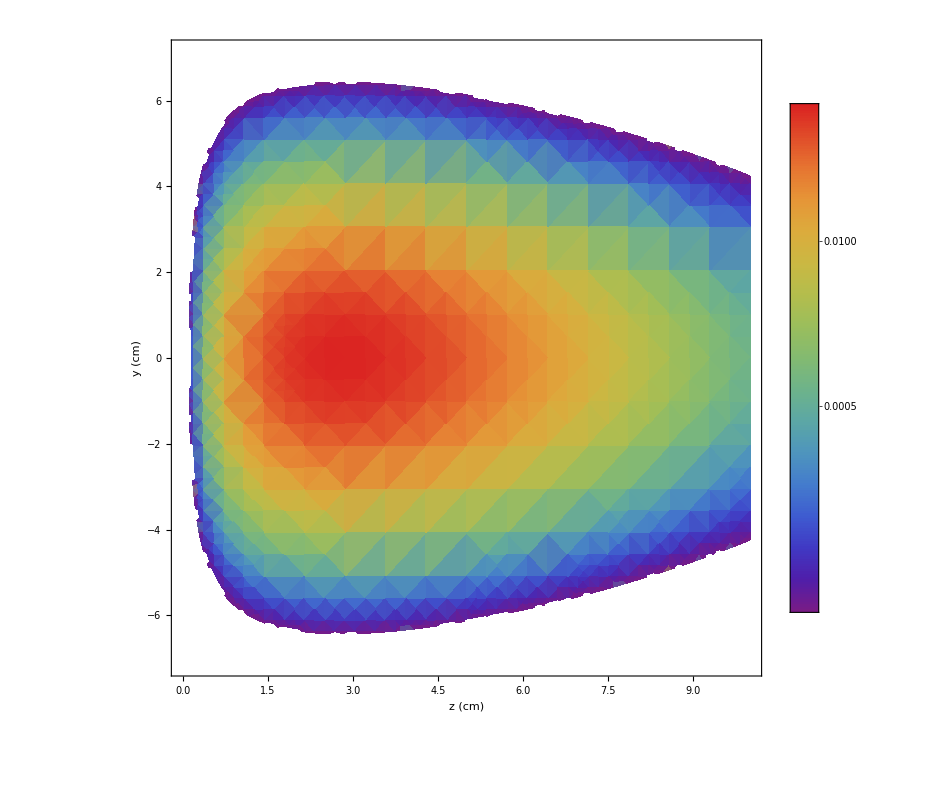

```mathematica
DensityPlot[powerDensity3D[x0,y,z],{z,z0-Lz/2,z0+Lz/2},{y,y0-Ly/2,y0+Ly/2},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z (cm)", "y (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

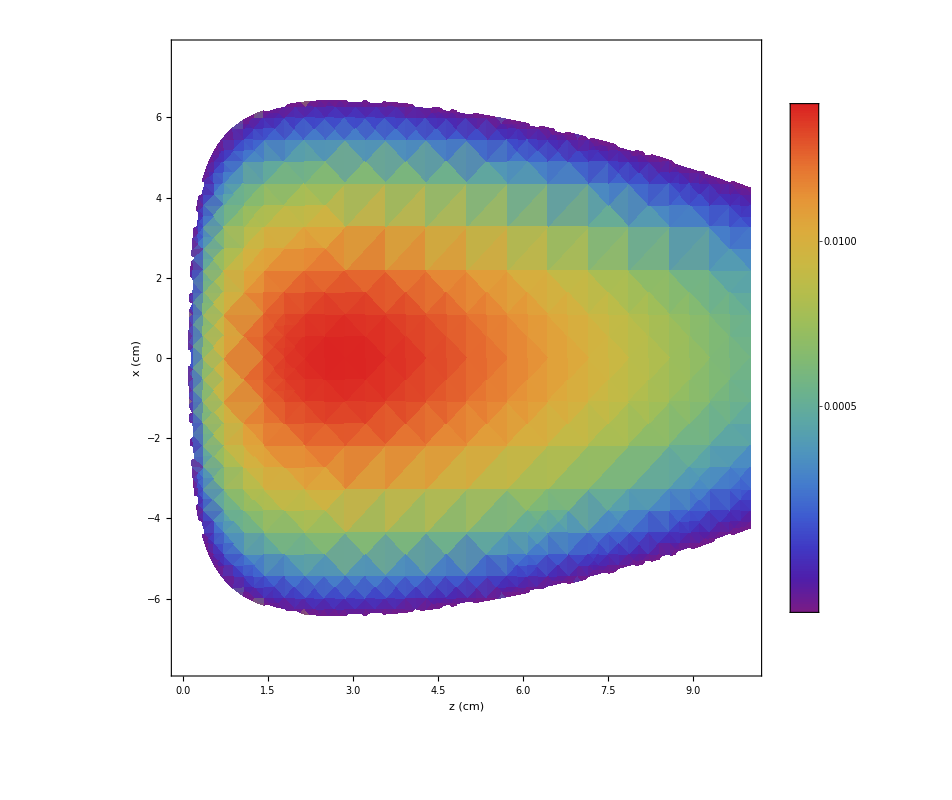

```mathematica
DensityPlot[powerDensity3D[x,x0,z],{z,z0-Lz/2,z0+Lz/2},{x,x0-Lx/2,x0+Lx/2},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z (cm)", "x (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

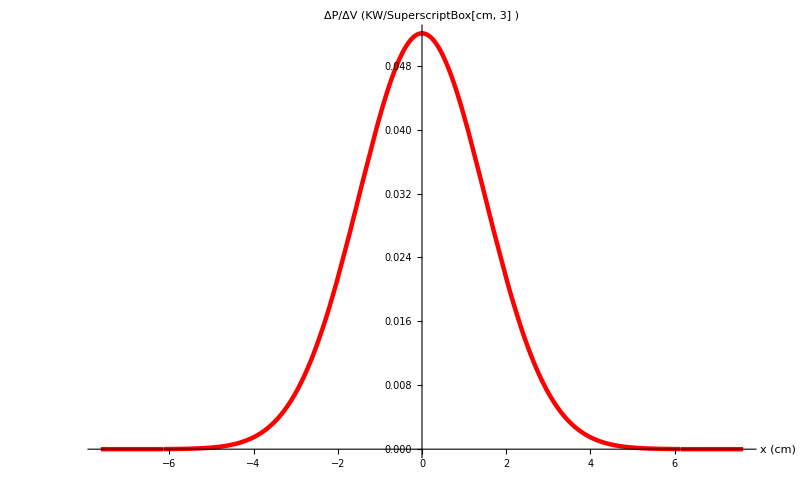

```mathematica
Plot[powerDensity3D[x,x0,z0],{x,x0-Lx/2,x0+Lx/2},AxesLabel->{"x (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

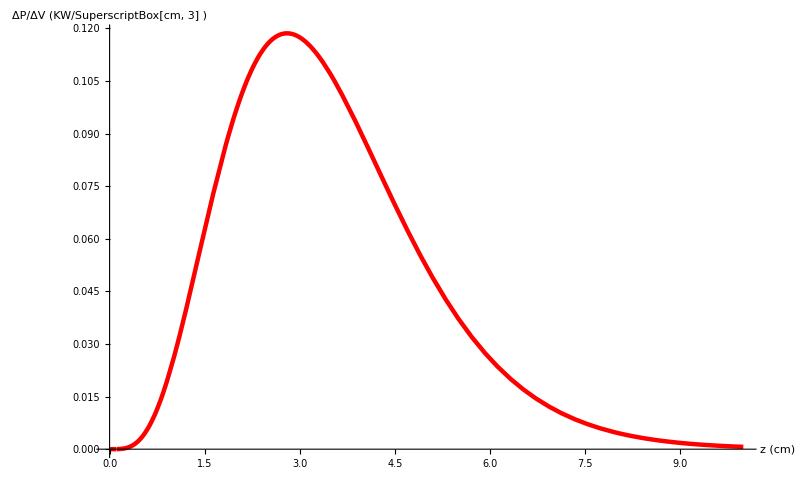

```mathematica
Plot[powerDensity3D[x0,y0,z],{z,z0-Lz/2,z0+Lz/2}, AxesLabel->{"z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

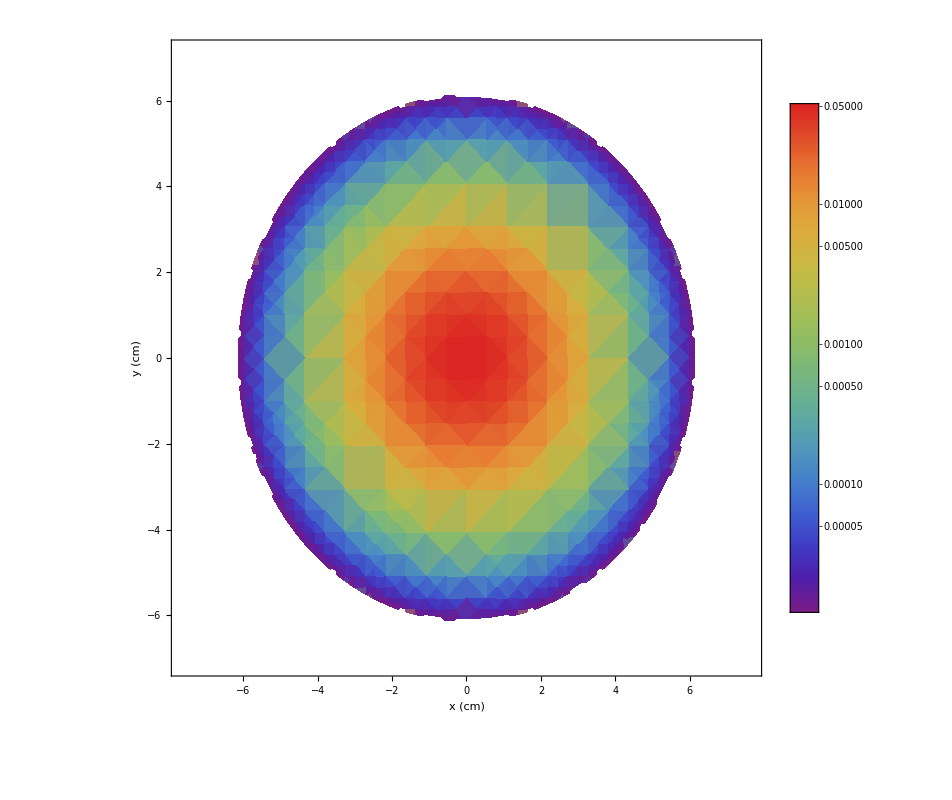

```mathematica
DensityPlot[powerDensity3D[x,y,z0],{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

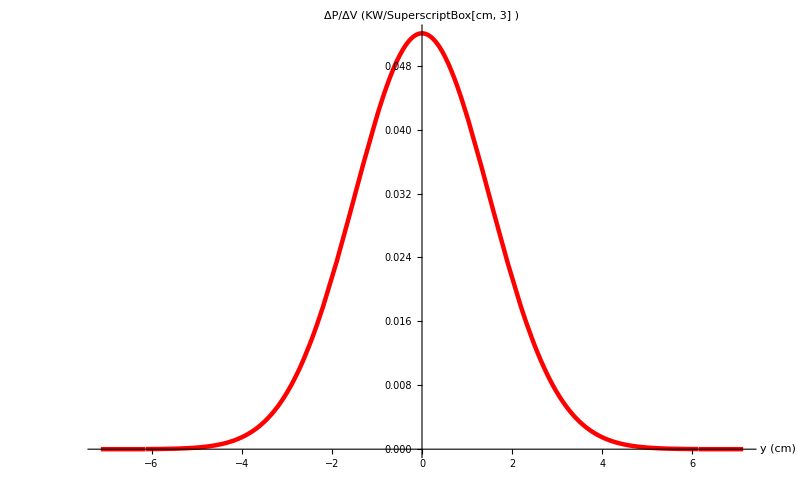

```mathematica
Plot[powerDensity3D[x0,y,z0],{y,y0-Ly/2,y0+Ly/2},AxesLabel->{"y (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
(*tungstenRectangularRegion=Cuboid[{x0-Lx/2,y0-Ly/2,z0-Lz/2},{x0+Lx/2,y0+Ly/2,z0+Lz/2}];*)
(*RegionPlot3D[tungstenRectangularRegion,AxesLabel->Automatic,PerformanceGoal->"Speed",Mesh->None]*)
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x,y,z}∈RegionBoundary@ tungstenRectangularRegion] ;*)
```

```mathematica
(*sol=NDSolveValue[{eqn,DirichletCondition[ u[x,y,z]==T0, {x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2}] }, u,{x, y,z} ∈ tungstenRectangularRegion]*)
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2||z==z0-Lz/2||z==z0+Lz/2}] ;*)
```

```mathematica
(*sol=NDSolveValue[{eqn,u[x0-Lx/2,y,z]==T0, u[x0+Lx/2,y,z]==T0,u[x,y0-Ly/2,z]==T0,u[x,y0+Ly/2,z]==T0  }, u,{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2||z==z0-Lz/2||z==z0+Lz/2}] + NeumannValue[-α/kappa*(u[x,y,z]-T0), x==x0-Lx/2||x==x0+Lx/2||y==y0-Ly/2||y==y0+Ly/2];
```

```mathematica
sol=NDSolveValue[eqn  , u,{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}]
```

```mathematica
(*solAn = DSolve[{eqn,u[x0-Lx/2,y,z]==T0, u[x0+Lx/2,y,z]==T0,u[x,y0-Ly/2,z]==T0,u[x,y0+Ly/2,z]==T0  }, u,{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}];*)
```

```mathematica
(*sol=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/Results4VitalysModel/tSolutionFunc_100degT0_goodResults.m"]*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/Results4VitalysModel/tSolutionFunc_100degT0_goodResults.m", sol]*)
```

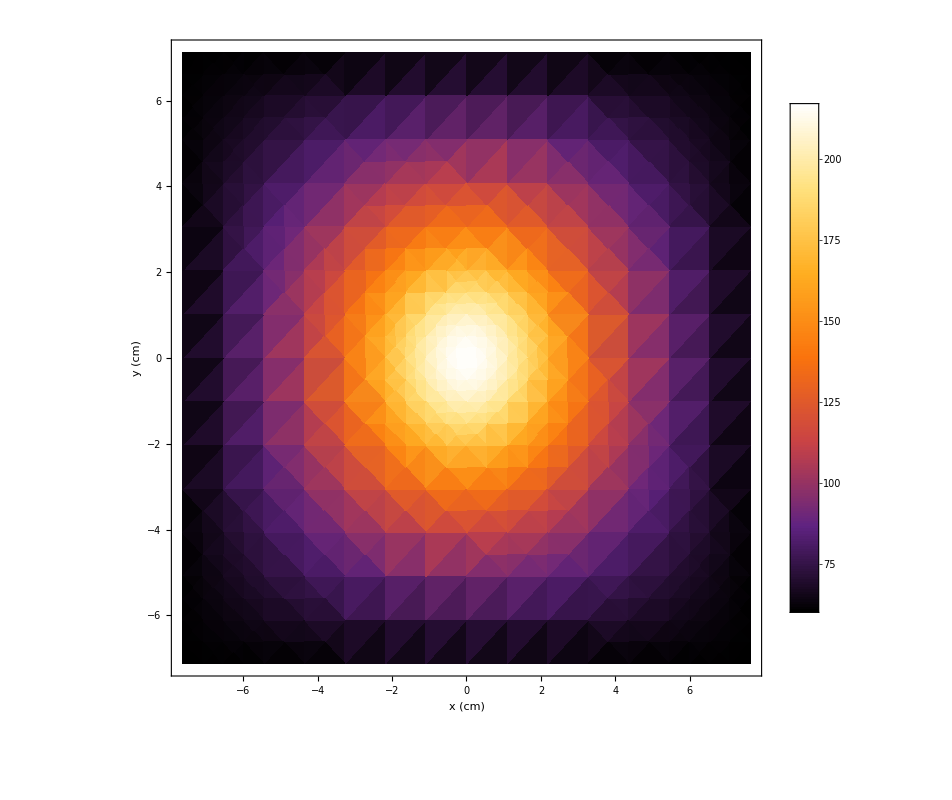

```mathematica
DensityPlot[sol[x,y,2.75], {x,x0-Lx/2,x0+Lx/2},{y,x0-Ly/2,x0+Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

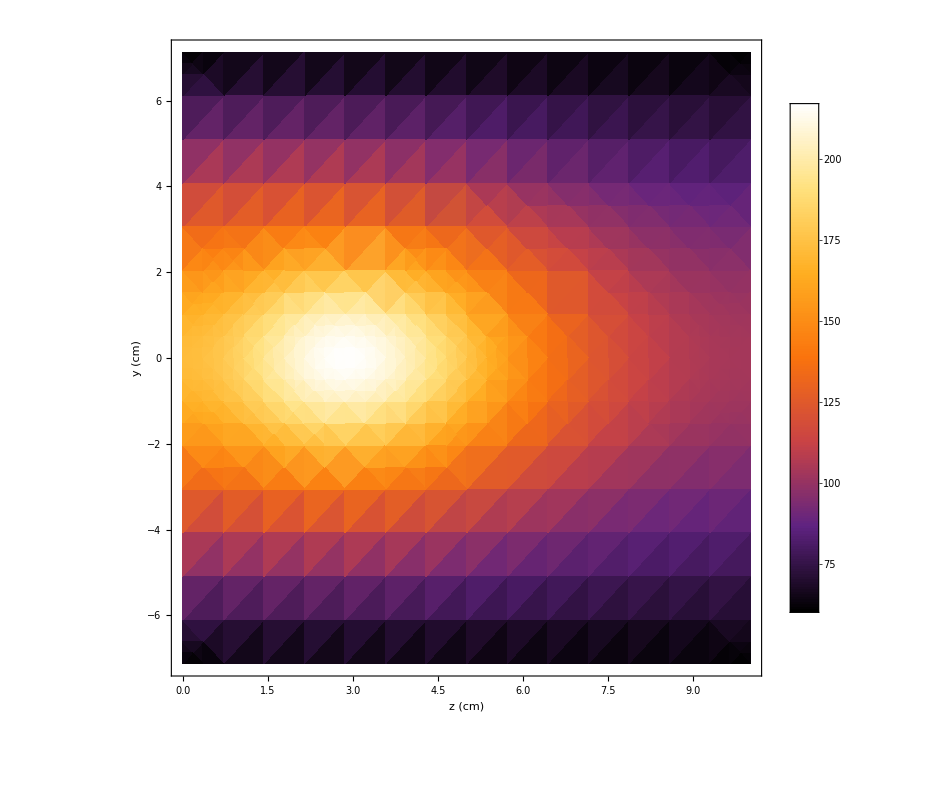

```mathematica
DensityPlot[sol[x0,y,z], {z,z0-Lz/2,z0+Lz/2},{y,y0-Ly/2,y0+Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{800,800},FrameLabel->{ "z (cm)", "y (cm)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

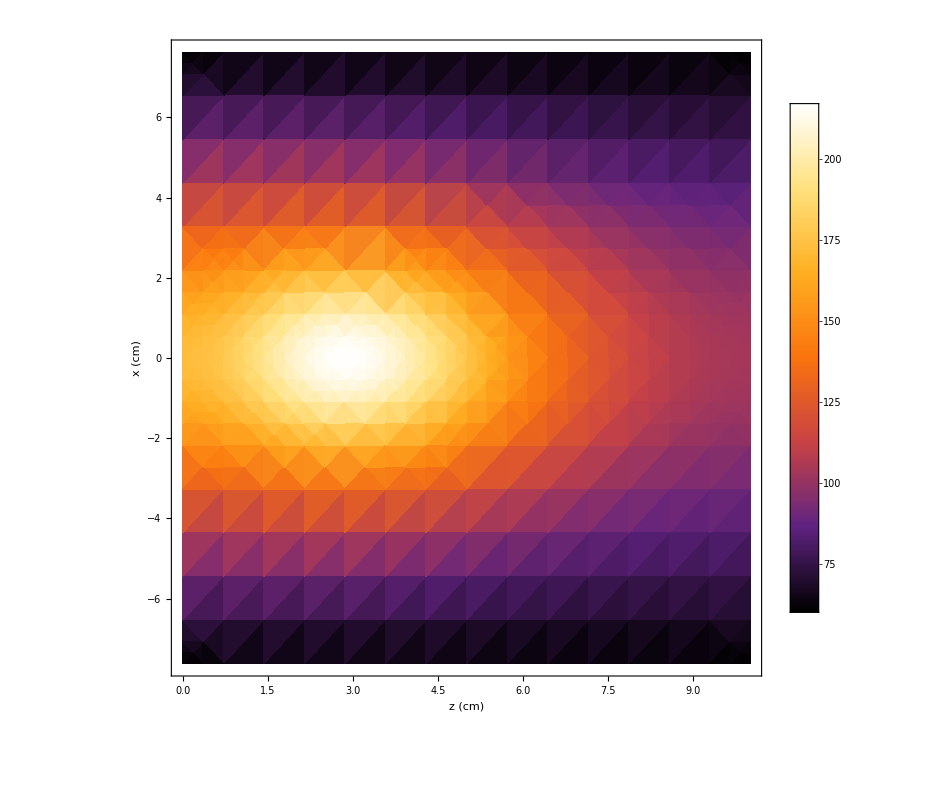

```mathematica
DensityPlot[sol[x,y0,z],{z,z0-Lz/2,z0+Lz/2},{x,x0-Lx/2,x0+Lx/2} ,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{800,800},FrameLabel->{ "z (cm)", "x (cm)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,x0-Lx/2,x0+Lx/2},{y,y0-Ly/2,y0+Ly/2},{z,z0-Lz/2,z0+Lz/2}, PlotTheme->"Detailed", ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "x (cm)", "y (cm)","z (cm)"},LabelStyle->{22,GrayLevel[0],Italic}]
```

-Graphics3D-

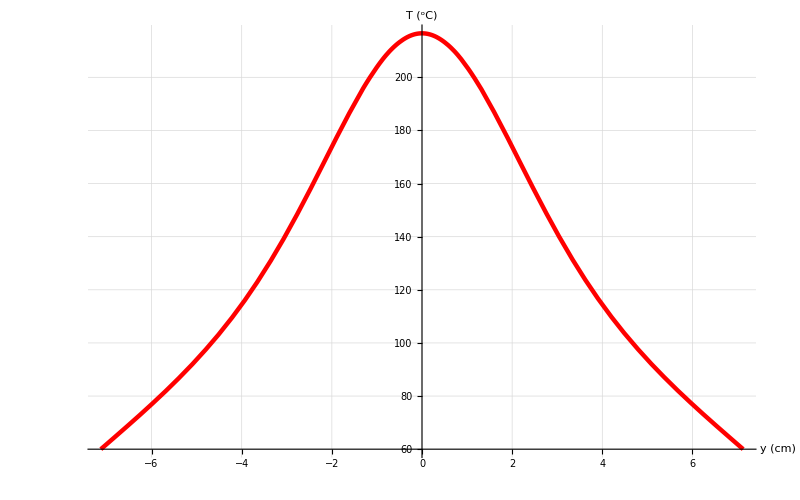

```mathematica
Plot[sol[x0,y,3], {y,y0-Ly/2,y0+Ly/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"y (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

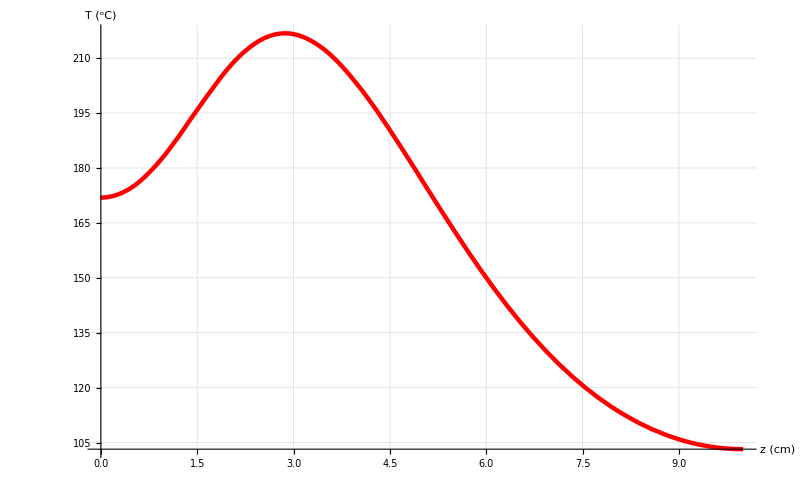

```mathematica
Plot[sol[x0,y0,z], {z,z0-Lz/2,z0+Lz/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

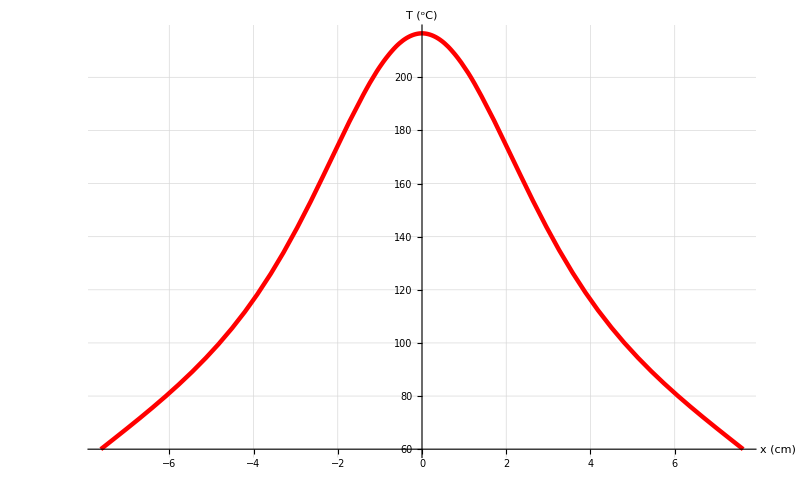

```mathematica
Plot[sol[x,y0,3], {x,x0-Lx/2,x0+Lx/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"x (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```